# Sphere Irradiance

Here we’re investigating a way to reduce the complexity of computing the irradiance provided by a sphere from a specific position outside the sphere. The point has a position and a normal and we’re especially interested in handling the horizon clipping situation.
The original analytical solution comes from Snyder, J. 1996 “Area Light Sources for Real-Time Graphics” (https://www.microsoft.com/en-us/research/publication/area-light-sources-for-real-time-graphics/).
It was later optimized by Sébastien Lagarde then analytically fitted by Stephen Hill and Eric Heitz but the fitting suffers from serious issues when the sphere goes below the horizon.

We thus need to find a better approximation!

Code

// Ref: Moving Frostbite to Physically Based Rendering, page 47 (2015, optimized).
// ‘sinSqSigma’ is the sine^2 of the real of the opening angle of the sphere as seen from the shaded point.
// ‘cosOmega’ is the cosine of the angle between the normal and the direction to the center of the light.
// N.b.: this function accounts for horizon clipping.
real DiffuseSphereLightIrradiance(real sinSqSigma, real cosOmega)
{
	real cosSqOmega = cosOmega * cosOmega;                     // y^2

	if (cosSqOmega > sinSqSigma)                                // (y^2)>x
            	return saturate(sinSqSigma * cosOmega);                 // Clip[x*y,{0,1}]
        	else
        	{
            real cotSqSigma = rcp(sinSqSigma) - 1;                 // 1/x-1
            real tanSqSigma = rcp(cotSqSigma);                     // x/(1-x)
            real sinSqOmega = 1 - cosSqOmega;                      // 1-y^2

            real w = sinSqOmega * tanSqSigma;                      // (1-y^2)*(x/(1-x))
            real x = -cosOmega * rsqrt(w);                         // -y*Sqrt[(1/x-1)/(1-y^2)]
            real y = sqrt(sinSqOmega * tanSqSigma - cosSqOmega);   // Sqrt[(1-y^2)*(x/(1-x))-y^2]
            real z = y * cotSqSigma;                               // Sqrt[(1-y^2)*(x/(1-x))-y^2]*(1/x-1)

            real a = cosOmega * acos(x) - z;                       // y*ArcCos[-y*Sqrt[(1/x-1)/(1-y^2)]]-Sqrt[(1-y^2)*(x/(1-x))-y^2]*(1/x-1)
            real b = atan(y);                                      // ArcTan[Sqrt[(1-y^2)*(x/(1-x))-y^2]]

            return saturate(INV_PI * (a * sinSqSigma + b));
        }
}

Function

```mathematica
irradiance:=Function[{cosOmega,sqSinSigma},
(*sqCosOmega = cosOmega*cosOmega;
sqSinOmega=1-sqCosOmega;
sqCosSigma=1-sqSinSigma;
sqTanSigma = sqSinSigma / sqCosSigma;
σ=ArcSin[√sqSinSigma];
sqTanSigma=Tan[σ]^2;

w=sqSinOmega * sqTanSigma;
x=-cosOmega/(√w);
y=√(sqSinOmega*sqTanSigma-sqCosOmega);
z=y/sqTanSigma;
*)

ω=ArcCos[cosOmega];
σ=Min[π/2-0.000001,ArcSin[√Min[1,sqSinSigma]]];
w=Sin[ω]*Tan[σ];
x=(-Cos[ω])/w;
y=√(w*w-Cos[ω]^2);
z=y/Tan[σ]^2;

a=Cos[ω]*ArcCos[x]-z;
b=ArcTan[y];

result=If[Cos[ω]^2>Sin[σ]^2,
 Sin[σ]^2*Cos[ω], (* Clip[x*y,{0,1}] *)
(Sin[σ]^2*a+b)/π
];
Clip[ Re[result],{0,1}]
]
irradiance[Cos[π/4],Sin[π/8]^2]
irradiance[Cos[π/4],10]
```

Sin[π/8]^2/(√2)

0.853553

```mathematica
Plot3D[irradiance[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2}]
```

-Graphics3D-

```mathematica
Plot3D[irradiance[Cosθ,SqSinσ],{Cosθ,1,-1},{SqSinσ,0,1},PlotRange->{0,1}]
```

-Graphics3D-

Current Approximation

```mathematica
irradianceApprox1:=Function[{cosOmega,sqSinSigma},
x=sqSinSigma;
y=cosOmega;
x*(0.9245867471551246+y)*(0.5+(-0.9245867471551246+y)*(0.5359050373687144+x*(-1.0054221851257754+x*(1.8199061187417047-x*1.3172081704209504))))
]
```

```mathematica
Plot3D[irradianceApprox1[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2}]
```

-Graphics3D-

```mathematica
Show[Plot3D[irradiance[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotRange->{-0.1,1}],Plot3D[irradianceApprox1[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotStyle->Red]]
```

-Graphics3D-

New Fitting

The following plot is almost a bilinear interpolation when x=Cos(θ) and y=(Sin(σ))^2:

```mathematica
Plot3D[irradiance[Cosθ,SqSinσ],{Cosθ,-1,1},{SqSinσ,0,1},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
(*ta=Flatten[Table[{CosTheta,SqSinSigma,irradiance[CosTheta,SqSinSigma]},{CosTheta,-1,0.98,0.02},{SqSinSigma,0,0.99,0.01}],1];*)
ta=Flatten[Table[{(1+CosTheta)/2,SqSinSigma,irradiance[CosTheta,SqSinSigma]},{CosTheta,-0.9,0.9,0.2},{SqSinSigma,0,0.9,0.1}],1];
ta=Flatten[Table[{(1+CosTheta)/2,SqSinSigma,irradiance[CosTheta,SqSinSigma]},{CosTheta,-0.99,1,0.02},{SqSinSigma,0,0.999,0.01}],1];

(* Actual table *)
(*ta=Flatten[Table[{CosTheta,SqSinSigma,irradiance[CosTheta,SqSinSigma]},{CosTheta,-0.99,0.99,0.05},{SqSinSigma,0,0.98,0.02}],1];*)

Length[ta]
```

10000

```mathematica
ListPlot3D[ta,PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Clear[a,b,c,d,e,x,y]

(*fit=NonlinearModelFit[ta,model,{a,b,c,d,e},{x,y}];*)
(*Normal[fit]*)

model=a+b*x+c*y+d*x*y;
model=y*(x+e)*(0.5+(x-e)*(a+b*y+c*y^2+d*y^3)); (* Heitz Model *)
model=y*(1+x)/2*(a+b*(1+x)/2+c*y+d*(1+x)/2*y);
model=a*(1+x)/2*y+b*((1+x)/2)^2*y+c*(1+x)/2*y^2+d*((1+x)/2)^2*y^2;
model=a*x*y+b*x^2*y+c*x*y^2+d*x^2*y^2;

fit=FindFit[ta,model,{a,b,c,d,e},{x,y}]
irradianceApprox2=Function[{x,y},Evaluate[model/.fit]]

Normal[NonlinearModelFit[ta,model,{a,b,c,d,e},{x,y}]]

(*fit={a->-1,b->2,c->π/2,d->-π/2}*)

(*Show[Plot3D[model/.fit,{x,-1,1},{y,0,1},PlotRange->All,AxesLabel->{"x","y"}],ListPointPlot3D[ta,PlotStyle->Directive[PointSize[Medium],Red]]]*)
Show[Plot3D[irradianceApprox2[x,y],{x,0,1},{y,0,1},PlotRange->All,AxesLabel->{"x","y"}],
ListPointPlot3D[ta,PlotStyle->Directive[PointSize[Tiny],Red]]]
```

FindFit::fitd: First argument {{{-1., 0.}, {-0.95, 0.}, {-0.9, 0.}, {-0.85, 0.}, {-0.8, 0.}, {-0.75, 0.}, {-0.7, 0.}, {-0.65, 0.}, {-0.6, 0.}, {-0.55, 0.}, {-0.5, 0.}, {-0.45, 0.}, {-0.4, 0.}, {-0.35, 0.}, {-0.3, 0.}, {-0.25, 0.}, {-0.2, 0.}, {-0.15, 0.}, « 6 », {0.2, 0.}, {0.25, 0.}, {0.3, 0.}, {0.35, 0.}, {0.4, 0.}, {0.45, 0.}, {0.5, 0.}, {0.55, 0.}, {0.6, 0.}, {0.65, 0.}, {0.7, 0.}, {0.75, 0.}, {0.8, 0.}, {0.85, 0.}, {0.9, 0.}, {0.95, 0.}, {1., 0.}}, « 16 »} in FindFit is not a list or a rectangular array.

FindFit[{{{-1.,0.},{-0.95,0.},{-0.9,0.},{-0.85,0.},{-0.8,0.},{-0.75,0.},{-0.7,0.},{-0.65,0.},{-0.6,0.},{-0.55,0.},{-0.5,0.},{-0.45,0.},{-0.4,0.},{-0.35,0.},{-0.3,0.},{-0.25,0.},{-0.2,0.},{-0.15,0.},{-0.1,0.},{-0.05,0.},{0.,0.},{0.05,0.},{0.1,0.},{0.15,0.},{0.2,0.},{0.25,0.},{0.3,0.},{0.35,0.},{0.4,0.},{0.45,0.},{0.5,0.},{0.55,0.},{0.6,0.},{0.65,0.},{0.7,0.},{0.75,0.},{0.8,0.},{0.85,0.},{0.9,0.},{0.95,0.},{1.,0.}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0},{-0.35,0},{-0.3,0},{-0.25,0.},{-0.2,0.0000708},{-0.15,0.000384288},{-0.1,0.00101763},{-0.05,0.00200971},{0.,0.00338007},{0.05,0.00513471},{0.1,0.00726763},{0.15,0.00975929},{0.2,0.0125708},{0.25,0.015625},{0.3,0.01875},{0.35,0.021875},{0.4,0.025},{0.45,0.028125},{0.5,0.03125},{0.55,0.034375},{0.6,0.0375},{0.65,0.040625},{0.7,0.04375},{0.75,0.046875},{0.8,0.05},{0.85,0.053125},{0.9,0.05625},{0.95,0.059375},{1.,0.0625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0},{-0.35,1.30814×10^-7},{-0.3,0.000109964},{-0.25,0.000546758},{-0.2,0.00140388},{-0.15,0.00273037},{-0.1,0.00455474},{-0.05,0.00689359},{0.,0.00975563},{0.05,0.0131436},{0.1,0.0170547},{0.15,0.0214804},{0.2,0.0264039},{0.25,0.0317968},{0.3,0.03761},{0.35,0.0437501},{0.4,0.05},{0.45,0.05625},{0.5,0.0625},{0.55,0.06875},{0.6,0.075},{0.65,0.08125},{0.7,0.0875},{0.75,0.09375},{0.8,0.1},{0.85,0.10625},{0.9,0.1125},{0.95,0.11875},{1.,0.125}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0.0000411512},{-0.35,0.000391362},{-0.3,0.00121105},{-0.25,0.00256928},{-0.2,0.00450334},{-0.15,0.00703453},{-0.1,0.0101752},{-0.05,0.0139322},{0.,0.0183092},{0.05,0.0233072},{0.1,0.0289252},{0.15,0.0351595},{0.2,0.0420033},{0.25,0.0494443},{0.3,0.057461},{0.35,0.0660164},{0.4,0.0750412},{0.45,0.084375},{0.5,0.09375},{0.55,0.103125},{0.6,0.1125},{0.65,0.121875},{0.7,0.13125},{0.75,0.140625},{0.8,0.15},{0.85,0.159375},{0.9,0.16875},{0.95,0.178125},{1.,0.1875}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0.},{-0.45,0.000136936},{-0.4,0.000729921},{-0.35,0.00190417},{-0.3,0.00371543},{-0.25,0.00619139},{-0.2,0.00934583},{-0.15,0.0131853},{-0.1,0.0177127},{-0.05,0.022929},{0.,0.0288344},{0.05,0.035429},{0.1,0.0427127},{0.15,0.0506853},{0.2,0.0593458},{0.25,0.0686914},{0.3,0.0787154},{0.35,0.0894042},{0.4,0.10073},{0.45,0.112637},{0.5,0.125},{0.55,0.1375},{0.6,0.15},{0.65,0.1625},{0.7,0.175},{0.75,0.1875},{0.8,0.2},{0.85,0.2125},{0.9,0.225},{0.95,0.2375},{1.,0.25}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,2.39701×10^-6},{-0.5,0.000243941},{-0.45,0.00105752},{-0.4,0.00255457},{-0.35,0.00477991},{-0.3,0.00775131},{-0.25,0.0114739},{-0.2,0.0159471},{-0.15,0.0211677},{-0.1,0.0271321},{-0.05,0.0338372},{0.,0.0412808},{0.05,0.0494622},{0.1,0.0583821},{0.15,0.0680427},{0.2,0.0784471},{0.25,0.0895989},{0.3,0.101501},{0.35,0.114155},{0.4,0.127555},{0.45,0.141683},{0.5,0.156494},{0.55,0.171877},{0.6,0.1875},{0.65,0.203125},{0.7,0.21875},{0.75,0.234375},{0.8,0.25},{0.85,0.265625},{0.9,0.28125},{0.95,0.296875},{1.,0.3125}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,6.32943×10^-6},{-0.55,0.0003316},{-0.5,0.00133751},{-0.45,0.00312925},{-0.4,0.00574059},{-0.35,0.0091779},{-0.3,0.013436},{-0.25,0.0185051},{-0.2,0.0243746},{-0.15,0.0310345},{-0.1,0.0384763},{-0.05,0.0466939},{0.,0.0556836},{0.05,0.0654439},{0.1,0.0759763},{0.15,0.0872845},{0.2,0.0993746},{0.25,0.112255},{0.3,0.125936},{0.35,0.140428},{0.4,0.155741},{0.45,0.171879},{0.5,0.188838},{0.55,0.206582},{0.6,0.225006},{0.65,0.24375},{0.7,0.2625},{0.75,0.28125},{0.8,0.3},{0.85,0.31875},{0.9,0.3375},{0.95,0.35625},{1.,0.375}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,6.31864×10^-6},{-0.6,0.000382481},{-0.55,0.00155051},{-0.5,0.00361433},{-0.45,0.00659493},{-0.4,0.0104846},{-0.35,0.0152652},{-0.3,0.020916},{-0.25,0.0274166},{-0.2,0.0347492},{-0.15,0.0428986},{-0.1,0.0518531},{-0.05,0.0616042},{0.,0.0721468},{0.05,0.0834792},{0.1,0.0956031},{0.15,0.108524},{0.2,0.122249},{0.25,0.136792},{0.3,0.152166},{0.35,0.16839},{0.4,0.185485},{0.45,0.20347},{0.5,0.222364},{0.55,0.242176},{0.6,0.262882},{0.65,0.284381},{0.7,0.30625},{0.75,0.328125},{0.8,0.35},{0.85,0.371875},{0.9,0.39375},{0.95,0.415625},{1.,0.4375}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,2.38762×10^-6},{-0.65,0.000388451},{-0.6,0.0016869},{-0.55,0.00400655},{-0.5,0.00735206},{-0.45,0.0116973},{-0.4,0.0170078},{-0.35,0.0232485},{-0.3,0.0303875},{-0.25,0.0383971},{-0.2,0.047254},{-0.15,0.0569395},{-0.1,0.0674393},{-0.05,0.0787431},{0.,0.0908451},{0.05,0.103743},{0.1,0.117439},{0.15,0.13194},{0.2,0.147254},{0.25,0.163397},{0.3,0.180387},{0.35,0.198248},{0.4,0.217008},{0.45,0.236697},{0.5,0.257352},{0.55,0.279007},{0.6,0.301687},{0.65,0.325388},{0.7,0.350002},{0.75,0.375},{0.8,0.4},{0.85,0.425},{0.9,0.45},{0.95,0.475},{1.,0.5}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0.000348388},{-0.65,0.00174274},{-0.6,0.00430942},{-0.55,0.00803045},{-0.5,0.0128545},{-0.45,0.0187252},{-0.4,0.0255895},{-0.35,0.0334009},{-0.3,0.0421198},{-0.25,0.0517129},{-0.2,0.0621535},{-0.15,0.0734202},{-0.1,0.0854969},{-0.05,0.0983723},{0.,0.11204},{0.05,0.126497},{0.1,0.141747},{0.15,0.157795},{0.2,0.174654},{0.25,0.192338},{0.3,0.21087},{0.35,0.230276},{0.4,0.25059},{0.45,0.27185},{0.5,0.294105},{0.55,0.317405},{0.6,0.341809},{0.65,0.367368},{0.7,0.394098},{0.75,0.421875},{0.8,0.45},{0.85,0.478125},{0.9,0.50625},{0.95,0.534375},{1.,0.5625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0.000267658},{-0.7,0.00171744},{-0.65,0.004532},{-0.6,0.00865956},{-0.55,0.0140123},{-0.5,0.0205037},{-0.45,0.028057},{-0.4,0.0366073},{-0.35,0.0461003},{-0.3,0.0564913},{-0.25,0.0677437},{-0.2,0.0798283},{-0.15,0.0927222},{-0.1,0.106408},{-0.05,0.120875},{0.,0.136114},{0.05,0.152125},{0.1,0.168908},{0.15,0.186472},{0.2,0.204828},{0.25,0.223994},{0.3,0.243991},{0.35,0.26485},{0.4,0.286607},{0.45,0.309307},{0.5,0.333004},{0.55,0.357762},{0.6,0.38366},{0.65,0.410782},{0.7,0.439217},{0.75,0.469018},{0.8,0.5},{0.85,0.53125},{0.9,0.5625},{0.95,0.59375},{1.,0.625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0.0001599},{-0.75,0.00161244},{-0.7,0.00469008},{-0.65,0.00928644},{-0.6,0.0152576},{-0.55,0.0224736},{-0.5,0.0308261},{-0.45,0.0402261},{-0.4,0.0506014},{-0.35,0.0618935},{-0.3,0.0740548},{-0.25,0.0870473},{-0.2,0.100841},{-0.15,0.115411},{-0.1,0.130742},{-0.05,0.14682},{0.,0.163638},{0.05,0.181195},{0.1,0.199492},{0.15,0.218536},{0.2,0.238341},{0.25,0.258922},{0.3,0.280305},{0.35,0.302518},{0.4,0.325601},{0.45,0.349601},{0.5,0.374576},{0.55,0.400599},{0.6,0.427758},{0.65,0.456161},{0.7,0.48594},{0.75,0.517237},{0.8,0.55016},{0.85,0.584375},{0.9,0.61875},{0.95,0.653125},{1.,0.6875}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0.0000529671},{-0.8,0.00143032},{-0.75,0.00481127},{-0.7,0.00999317},{-0.65,0.0167391},{-0.6,0.024854},{-0.55,0.034185},{-0.5,0.0446122},{-0.45,0.0560414},{-0.4,0.0683977},{-0.35,0.0816213},{-0.3,0.0956643},{-0.25,0.110489},{-0.2,0.126064},{-0.15,0.142368},{-0.1,0.159383},{-0.05,0.177096},{0.,0.195501},{0.05,0.214596},{0.1,0.234383},{0.15,0.254868},{0.2,0.276064},{0.25,0.297989},{0.3,0.320664},{0.35,0.344121},{0.4,0.368398},{0.45,0.393541},{0.5,0.419612},{0.55,0.446685},{0.6,0.474854},{0.65,0.504239},{0.7,0.534993},{0.75,0.567311},{0.8,0.60143},{0.85,0.637553},{0.9,0.675},{0.95,0.7125},{1.,0.75}},{{-1.,0},{-0.95,0},{-0.9,1.99131×10^-7},{-0.85,0.00117437},{-0.8,0.00495135},{-0.75,0.0109448},{-0.7,0.0187481},{-0.65,0.0280627},{-0.6,0.0386724},{-0.55,0.0504171},{-0.5,0.0631757},{-0.45,0.0768549},{-0.4,0.0913816},{-0.35,0.106698},{-0.3,0.122759},{-0.25,0.139528},{-0.2,0.156977},{-0.15,0.175083},{-0.1,0.193831},{-0.05,0.213209},{0.,0.23321},{0.05,0.253834},{0.1,0.275081},{0.15,0.296958},{0.2,0.319477},{0.25,0.342653},{0.3,0.366509},{0.35,0.391073},{0.4,0.416382},{0.45,0.44248},{0.5,0.469426},{0.55,0.497292},{0.6,0.526172},{0.65,0.556188},{0.7,0.587498},{0.75,0.62032},{0.8,0.654951},{0.85,0.691799},{0.9,0.73125},{0.95,0.771875},{1.,0.8125}},{{-1.,0},{-0.95,0},{-0.9,0.000848165},{-0.85,0.00525433},{-0.8,0.0125505},{-0.75,0.021975},{-0.7,0.0330561},{-0.65,0.0454872},{-0.6,0.059058},{-0.55,0.0736179},{-0.5,0.0890551},{-0.45,0.105285},{-0.4,0.122241},{-0.35,0.139873},{-0.3,0.158139},{-0.25,0.177008},{-0.2,0.196454},{-0.15,0.216459},{-0.1,0.237007},{-0.05,0.258091},{0.,0.279702},{0.05,0.301841},{0.1,0.324507},{0.15,0.347709},{0.2,0.371454},{0.25,0.395758},{0.3,0.420639},{0.35,0.446123},{0.4,0.472241},{0.45,0.499035},{0.5,0.526555},{0.55,0.554868},{0.6,0.584058},{0.65,0.614237},{0.7,0.645556},{0.75,0.678225},{0.8,0.71255},{0.85,0.749004},{0.9,0.788348},{0.95,0.83125},{1.,0.875}},{{-1.,0},{-0.95,0.000455462},{-0.9,0.00629309},{-0.85,0.0162656},{-0.8,0.0286978},{-0.75,0.0428301},{-0.7,0.0582476},{-0.65,0.0746953},{-0.6,0.0920031},{-0.55,0.110052},{-0.5,0.128754},{-0.45,0.148044},{-0.4,0.167871},{-0.35,0.188196},{-0.3,0.208988},{-0.25,0.230223},{-0.2,0.251882},{-0.15,0.27395},{-0.1,0.296416},{-0.05,0.319274},{0.,0.342519},{0.05,0.366149},{0.1,0.390166},{0.15,0.414575},{0.2,0.439382},{0.25,0.464598},{0.3,0.490238},{0.35,0.516321},{0.4,0.542871},{0.45,0.569919},{0.5,0.597504},{0.55,0.625677},{0.6,0.654503},{0.65,0.68407},{0.7,0.714498},{0.75,0.745955},{0.8,0.778698},{0.85,0.813141},{0.9,0.850043},{0.95,0.89108},{1.,0.9375}},{{-1.,0},{-0.95,0.0249998},{-0.9,0.0499997},{-0.85,0.0749997},{-0.8,0.0999996},{-0.75,0.125},{-0.7,0.15},{-0.65,0.175},{-0.6,0.199999},{-0.55,0.224999},{-0.5,0.249999},{-0.45,0.274999},{-0.4,0.299999},{-0.35,0.324999},{-0.3,0.349999},{-0.25,0.374999},{-0.2,0.399999},{-0.15,0.424999},{-0.1,0.449999},{-0.05,0.474999},{0.,0.499999},{0.05,0.524999},{0.1,0.549999},{0.15,0.574999},{0.2,0.599999},{0.25,0.624999},{0.3,0.649999},{0.35,0.674999},{0.4,0.699999},{0.45,0.724999},{0.5,0.749999},{0.55,0.774999},{0.6,0.799999},{0.65,0.825},{0.7,0.85},{0.75,0.875},{0.8,0.9},{0.85,0.925},{0.9,0.95},{0.95,0.975},{1.,1.}}},a x y+b x^2 y+c x y^2+d x^2 y^2,{a,b,c,d,e},{x,y}]

FindFit::fitd: First argument {{{-1., 0.}, {-0.95, 0.}, {-0.9, 0.}, {-0.85, 0.}, {-0.8, 0.}, {-0.75, 0.}, {-0.7, 0.}, {-0.65, 0.}, {-0.6, 0.}, {-0.55, 0.}, {-0.5, 0.}, {-0.45, 0.}, {-0.4, 0.}, {-0.35, 0.}, {-0.3, 0.}, {-0.25, 0.}, {-0.2, 0.}, {-0.15, 0.}, « 6 », {0.2, 0.}, {0.25, 0.}, {0.3, 0.}, {0.35, 0.}, {0.4, 0.}, {0.45, 0.}, {0.5, 0.}, {0.55, 0.}, {0.6, 0.}, {0.65, 0.}, {0.7, 0.}, {0.75, 0.}, {0.8, 0.}, {0.85, 0.}, {0.9, 0.}, {0.95, 0.}, {1., 0.}}, « 16 »} in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Function[{x,y},a x y+b x^2 y+c x y^2+d x^2 y^2/.FindFit[{{{-1.,0.},{-0.95,0.},{-0.9,0.},{-0.85,0.},{-0.8,0.},{-0.75,0.},{-0.7,0.},{-0.65,0.},{-0.6,0.},{-0.55,0.},{-0.5,0.},{-0.45,0.},{-0.4,0.},{-0.35,0.},{-0.3,0.},{-0.25,0.},{-0.2,0.},{-0.15,0.},{-0.1,0.},{-0.05,0.},{0.,0.},{0.05,0.},{0.1,0.},{0.15,0.},{0.2,0.},{0.25,0.},{0.3,0.},{0.35,0.},{0.4,0.},{0.45,0.},{0.5,0.},{0.55,0.},{0.6,0.},{0.65,0.},{0.7,0.},{0.75,0.},{0.8,0.},{0.85,0.},{0.9,0.},{0.95,0.},{1.,0.}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0},{-0.35,0},{-0.3,0},{-0.25,0.},{-0.2,0.0000708},{-0.15,0.000384288},{-0.1,0.00101763},{-0.05,0.00200971},{0.,0.00338007},{0.05,0.00513471},{0.1,0.00726763},{0.15,0.00975929},{0.2,0.0125708},{0.25,0.015625},{0.3,0.01875},{0.35,0.021875},{0.4,0.025},{0.45,0.028125},{0.5,0.03125},{0.55,0.034375},{0.6,0.0375},{0.65,0.040625},{0.7,0.04375},{0.75,0.046875},{0.8,0.05},{0.85,0.053125},{0.9,0.05625},{0.95,0.059375},{1.,0.0625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0},{-0.35,1.30814×10^-7},{-0.3,0.000109964},{-0.25,0.000546758},{-0.2,0.00140388},{-0.15,0.00273037},{-0.1,0.00455474},{-0.05,0.00689359},{0.,0.00975563},{0.05,0.0131436},{0.1,0.0170547},{0.15,0.0214804},{0.2,0.0264039},{0.25,0.0317968},{0.3,0.03761},{0.35,0.0437501},{0.4,0.05},{0.45,0.05625},{0.5,0.0625},{0.55,0.06875},{0.6,0.075},{0.65,0.08125},{0.7,0.0875},{0.75,0.09375},{0.8,0.1},{0.85,0.10625},{0.9,0.1125},{0.95,0.11875},{1.,0.125}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0.0000411512},{-0.35,0.000391362},{-0.3,0.00121105},{-0.25,0.00256928},{-0.2,0.00450334},{-0.15,0.00703453},{-0.1,0.0101752},{-0.05,0.0139322},{0.,0.0183092},{0.05,0.0233072},{0.1,0.0289252},{0.15,0.0351595},{0.2,0.0420033},{0.25,0.0494443},{0.3,0.057461},{0.35,0.0660164},{0.4,0.0750412},{0.45,0.084375},{0.5,0.09375},{0.55,0.103125},{0.6,0.1125},{0.65,0.121875},{0.7,0.13125},{0.75,0.140625},{0.8,0.15},{0.85,0.159375},{0.9,0.16875},{0.95,0.178125},{1.,0.1875}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0.},{-0.45,0.000136936},{-0.4,0.000729921},{-0.35,0.00190417},{-0.3,0.00371543},{-0.25,0.00619139},{-0.2,0.00934583},{-0.15,0.0131853},{-0.1,0.0177127},{-0.05,0.022929},{0.,0.0288344},{0.05,0.035429},{0.1,0.0427127},{0.15,0.0506853},{0.2,0.0593458},{0.25,0.0686914},{0.3,0.0787154},{0.35,0.0894042},{0.4,0.10073},{0.45,0.112637},{0.5,0.125},{0.55,0.1375},{0.6,0.15},{0.65,0.1625},{0.7,0.175},{0.75,0.1875},{0.8,0.2},{0.85,0.2125},{0.9,0.225},{0.95,0.2375},{1.,0.25}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,2.39701×10^-6},{-0.5,0.000243941},{-0.45,0.00105752},{-0.4,0.00255457},{-0.35,0.00477991},{-0.3,0.00775131},{-0.25,0.0114739},{-0.2,0.0159471},{-0.15,0.0211677},{-0.1,0.0271321},{-0.05,0.0338372},{0.,0.0412808},{0.05,0.0494622},{0.1,0.0583821},{0.15,0.0680427},{0.2,0.0784471},{0.25,0.0895989},{0.3,0.101501},{0.35,0.114155},{0.4,0.127555},{0.45,0.141683},{0.5,0.156494},{0.55,0.171877},{0.6,0.1875},{0.65,0.203125},{0.7,0.21875},{0.75,0.234375},{0.8,0.25},{0.85,0.265625},{0.9,0.28125},{0.95,0.296875},{1.,0.3125}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,6.32943×10^-6},{-0.55,0.0003316},{-0.5,0.00133751},{-0.45,0.00312925},{-0.4,0.00574059},{-0.35,0.0091779},{-0.3,0.013436},{-0.25,0.0185051},{-0.2,0.0243746},{-0.15,0.0310345},{-0.1,0.0384763},{-0.05,0.0466939},{0.,0.0556836},{0.05,0.0654439},{0.1,0.0759763},{0.15,0.0872845},{0.2,0.0993746},{0.25,0.112255},{0.3,0.125936},{0.35,0.140428},{0.4,0.155741},{0.45,0.171879},{0.5,0.188838},{0.55,0.206582},{0.6,0.225006},{0.65,0.24375},{0.7,0.2625},{0.75,0.28125},{0.8,0.3},{0.85,0.31875},{0.9,0.3375},{0.95,0.35625},{1.,0.375}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,6.31864×10^-6},{-0.6,0.000382481},{-0.55,0.00155051},{-0.5,0.00361433},{-0.45,0.00659493},{-0.4,0.0104846},{-0.35,0.0152652},{-0.3,0.020916},{-0.25,0.0274166},{-0.2,0.0347492},{-0.15,0.0428986},{-0.1,0.0518531},{-0.05,0.0616042},{0.,0.0721468},{0.05,0.0834792},{0.1,0.0956031},{0.15,0.108524},{0.2,0.122249},{0.25,0.136792},{0.3,0.152166},{0.35,0.16839},{0.4,0.185485},{0.45,0.20347},{0.5,0.222364},{0.55,0.242176},{0.6,0.262882},{0.65,0.284381},{0.7,0.30625},{0.75,0.328125},{0.8,0.35},{0.85,0.371875},{0.9,0.39375},{0.95,0.415625},{1.,0.4375}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,2.38762×10^-6},{-0.65,0.000388451},{-0.6,0.0016869},{-0.55,0.00400655},{-0.5,0.00735206},{-0.45,0.0116973},{-0.4,0.0170078},{-0.35,0.0232485},{-0.3,0.0303875},{-0.25,0.0383971},{-0.2,0.047254},{-0.15,0.0569395},{-0.1,0.0674393},{-0.05,0.0787431},{0.,0.0908451},{0.05,0.103743},{0.1,0.117439},{0.15,0.13194},{0.2,0.147254},{0.25,0.163397},{0.3,0.180387},{0.35,0.198248},{0.4,0.217008},{0.45,0.236697},{0.5,0.257352},{0.55,0.279007},{0.6,0.301687},{0.65,0.325388},{0.7,0.350002},{0.75,0.375},{0.8,0.4},{0.85,0.425},{0.9,0.45},{0.95,0.475},{1.,0.5}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0.000348388},{-0.65,0.00174274},{-0.6,0.00430942},{-0.55,0.00803045},{-0.5,0.0128545},{-0.45,0.0187252},{-0.4,0.0255895},{-0.35,0.0334009},{-0.3,0.0421198},{-0.25,0.0517129},{-0.2,0.0621535},{-0.15,0.0734202},{-0.1,0.0854969},{-0.05,0.0983723},{0.,0.11204},{0.05,0.126497},{0.1,0.141747},{0.15,0.157795},{0.2,0.174654},{0.25,0.192338},{0.3,0.21087},{0.35,0.230276},{0.4,0.25059},{0.45,0.27185},{0.5,0.294105},{0.55,0.317405},{0.6,0.341809},{0.65,0.367368},{0.7,0.394098},{0.75,0.421875},{0.8,0.45},{0.85,0.478125},{0.9,0.50625},{0.95,0.534375},{1.,0.5625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0.000267658},{-0.7,0.00171744},{-0.65,0.004532},{-0.6,0.00865956},{-0.55,0.0140123},{-0.5,0.0205037},{-0.45,0.028057},{-0.4,0.0366073},{-0.35,0.0461003},{-0.3,0.0564913},{-0.25,0.0677437},{-0.2,0.0798283},{-0.15,0.0927222},{-0.1,0.106408},{-0.05,0.120875},{0.,0.136114},{0.05,0.152125},{0.1,0.168908},{0.15,0.186472},{0.2,0.204828},{0.25,0.223994},{0.3,0.243991},{0.35,0.26485},{0.4,0.286607},{0.45,0.309307},{0.5,0.333004},{0.55,0.357762},{0.6,0.38366},{0.65,0.410782},{0.7,0.439217},{0.75,0.469018},{0.8,0.5},{0.85,0.53125},{0.9,0.5625},{0.95,0.59375},{1.,0.625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0.0001599},{-0.75,0.00161244},{-0.7,0.00469008},{-0.65,0.00928644},{-0.6,0.0152576},{-0.55,0.0224736},{-0.5,0.0308261},{-0.45,0.0402261},{-0.4,0.0506014},{-0.35,0.0618935},{-0.3,0.0740548},{-0.25,0.0870473},{-0.2,0.100841},{-0.15,0.115411},{-0.1,0.130742},{-0.05,0.14682},{0.,0.163638},{0.05,0.181195},{0.1,0.199492},{0.15,0.218536},{0.2,0.238341},{0.25,0.258922},{0.3,0.280305},{0.35,0.302518},{0.4,0.325601},{0.45,0.349601},{0.5,0.374576},{0.55,0.400599},{0.6,0.427758},{0.65,0.456161},{0.7,0.48594},{0.75,0.517237},{0.8,0.55016},{0.85,0.584375},{0.9,0.61875},{0.95,0.653125},{1.,0.6875}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0.0000529671},{-0.8,0.00143032},{-0.75,0.00481127},{-0.7,0.00999317},{-0.65,0.0167391},{-0.6,0.024854},{-0.55,0.034185},{-0.5,0.0446122},{-0.45,0.0560414},{-0.4,0.0683977},{-0.35,0.0816213},{-0.3,0.0956643},{-0.25,0.110489},{-0.2,0.126064},{-0.15,0.142368},{-0.1,0.159383},{-0.05,0.177096},{0.,0.195501},{0.05,0.214596},{0.1,0.234383},{0.15,0.254868},{0.2,0.276064},{0.25,0.297989},{0.3,0.320664},{0.35,0.344121},{0.4,0.368398},{0.45,0.393541},{0.5,0.419612},{0.55,0.446685},{0.6,0.474854},{0.65,0.504239},{0.7,0.534993},{0.75,0.567311},{0.8,0.60143},{0.85,0.637553},{0.9,0.675},{0.95,0.7125},{1.,0.75}},{{-1.,0},{-0.95,0},{-0.9,1.99131×10^-7},{-0.85,0.00117437},{-0.8,0.00495135},{-0.75,0.0109448},{-0.7,0.0187481},{-0.65,0.0280627},{-0.6,0.0386724},{-0.55,0.0504171},{-0.5,0.0631757},{-0.45,0.0768549},{-0.4,0.0913816},{-0.35,0.106698},{-0.3,0.122759},{-0.25,0.139528},{-0.2,0.156977},{-0.15,0.175083},{-0.1,0.193831},{-0.05,0.213209},{0.,0.23321},{0.05,0.253834},{0.1,0.275081},{0.15,0.296958},{0.2,0.319477},{0.25,0.342653},{0.3,0.366509},{0.35,0.391073},{0.4,0.416382},{0.45,0.44248},{0.5,0.469426},{0.55,0.497292},{0.6,0.526172},{0.65,0.556188},{0.7,0.587498},{0.75,0.62032},{0.8,0.654951},{0.85,0.691799},{0.9,0.73125},{0.95,0.771875},{1.,0.8125}},{{-1.,0},{-0.95,0},{-0.9,0.000848165},{-0.85,0.00525433},{-0.8,0.0125505},{-0.75,0.021975},{-0.7,0.0330561},{-0.65,0.0454872},{-0.6,0.059058},{-0.55,0.0736179},{-0.5,0.0890551},{-0.45,0.105285},{-0.4,0.122241},{-0.35,0.139873},{-0.3,0.158139},{-0.25,0.177008},{-0.2,0.196454},{-0.15,0.216459},{-0.1,0.237007},{-0.05,0.258091},{0.,0.279702},{0.05,0.301841},{0.1,0.324507},{0.15,0.347709},{0.2,0.371454},{0.25,0.395758},{0.3,0.420639},{0.35,0.446123},{0.4,0.472241},{0.45,0.499035},{0.5,0.526555},{0.55,0.554868},{0.6,0.584058},{0.65,0.614237},{0.7,0.645556},{0.75,0.678225},{0.8,0.71255},{0.85,0.749004},{0.9,0.788348},{0.95,0.83125},{1.,0.875}},{{-1.,0},{-0.95,0.000455462},{-0.9,0.00629309},{-0.85,0.0162656},{-0.8,0.0286978},{-0.75,0.0428301},{-0.7,0.0582476},{-0.65,0.0746953},{-0.6,0.0920031},{-0.55,0.110052},{-0.5,0.128754},{-0.45,0.148044},{-0.4,0.167871},{-0.35,0.188196},{-0.3,0.208988},{-0.25,0.230223},{-0.2,0.251882},{-0.15,0.27395},{-0.1,0.296416},{-0.05,0.319274},{0.,0.342519},{0.05,0.366149},{0.1,0.390166},{0.15,0.414575},{0.2,0.439382},{0.25,0.464598},{0.3,0.490238},{0.35,0.516321},{0.4,0.542871},{0.45,0.569919},{0.5,0.597504},{0.55,0.625677},{0.6,0.654503},{0.65,0.68407},{0.7,0.714498},{0.75,0.745955},{0.8,0.778698},{0.85,0.813141},{0.9,0.850043},{0.95,0.89108},{1.,0.9375}},{{-1.,0},{-0.95,0.0249998},{-0.9,0.0499997},{-0.85,0.0749997},{-0.8,0.0999996},{-0.75,0.125},{-0.7,0.15},{-0.65,0.175},{-0.6,0.199999},{-0.55,0.224999},{-0.5,0.249999},{-0.45,0.274999},{-0.4,0.299999},{-0.35,0.324999},{-0.3,0.349999},{-0.25,0.374999},{-0.2,0.399999},{-0.15,0.424999},{-0.1,0.449999},{-0.05,0.474999},{0.,0.499999},{0.05,0.524999},{0.1,0.549999},{0.15,0.574999},{0.2,0.599999},{0.25,0.624999},{0.3,0.649999},{0.35,0.674999},{0.4,0.699999},{0.45,0.724999},{0.5,0.749999},{0.55,0.774999},{0.6,0.799999},{0.65,0.825},{0.7,0.85},{0.75,0.875},{0.8,0.9},{0.85,0.925},{0.9,0.95},{0.95,0.975},{1.,1.}}},a x y+b x^2 y+c x y^2+d x^2 y^2,{a,b,c,d,e},{x,y}]]

NonlinearModelFit::fitd: First argument {{{-1., 0.}, {-0.95, 0.}, {-0.9, 0.}, {-0.85, 0.}, {-0.8, 0.}, {-0.75, 0.}, {-0.7, 0.}, {-0.65, 0.}, {-0.6, 0.}, {-0.55, 0.}, {-0.5, 0.}, {-0.45, 0.}, {-0.4, 0.}, {-0.35, 0.}, {-0.3, 0.}, {-0.25, 0.}, {-0.2, 0.}, {-0.15, 0.}, « 6 », {0.2, 0.}, {0.25, 0.}, {0.3, 0.}, {0.35, 0.}, {0.4, 0.}, {0.45, 0.}, {0.5, 0.}, {0.55, 0.}, {0.6, 0.}, {0.65, 0.}, {0.7, 0.}, {0.75, 0.}, {0.8, 0.}, {0.85, 0.}, {0.9, 0.}, {0.95, 0.}, {1., 0.}}, « 16 »} in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[{{{-1.,0.},{-0.95,0.},{-0.9,0.},{-0.85,0.},{-0.8,0.},{-0.75,0.},{-0.7,0.},{-0.65,0.},{-0.6,0.},{-0.55,0.},{-0.5,0.},{-0.45,0.},{-0.4,0.},{-0.35,0.},{-0.3,0.},{-0.25,0.},{-0.2,0.},{-0.15,0.},{-0.1,0.},{-0.05,0.},{0.,0.},{0.05,0.},{0.1,0.},{0.15,0.},{0.2,0.},{0.25,0.},{0.3,0.},{0.35,0.},{0.4,0.},{0.45,0.},{0.5,0.},{0.55,0.},{0.6,0.},{0.65,0.},{0.7,0.},{0.75,0.},{0.8,0.},{0.85,0.},{0.9,0.},{0.95,0.},{1.,0.}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0},{-0.35,0},{-0.3,0},{-0.25,0.},{-0.2,0.0000708},{-0.15,0.000384288},{-0.1,0.00101763},{-0.05,0.00200971},{0.,0.00338007},{0.05,0.00513471},{0.1,0.00726763},{0.15,0.00975929},{0.2,0.0125708},{0.25,0.015625},{0.3,0.01875},{0.35,0.021875},{0.4,0.025},{0.45,0.028125},{0.5,0.03125},{0.55,0.034375},{0.6,0.0375},{0.65,0.040625},{0.7,0.04375},{0.75,0.046875},{0.8,0.05},{0.85,0.053125},{0.9,0.05625},{0.95,0.059375},{1.,0.0625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0},{-0.35,1.30814×10^-7},{-0.3,0.000109964},{-0.25,0.000546758},{-0.2,0.00140388},{-0.15,0.00273037},{-0.1,0.00455474},{-0.05,0.00689359},{0.,0.00975563},{0.05,0.0131436},{0.1,0.0170547},{0.15,0.0214804},{0.2,0.0264039},{0.25,0.0317968},{0.3,0.03761},{0.35,0.0437501},{0.4,0.05},{0.45,0.05625},{0.5,0.0625},{0.55,0.06875},{0.6,0.075},{0.65,0.08125},{0.7,0.0875},{0.75,0.09375},{0.8,0.1},{0.85,0.10625},{0.9,0.1125},{0.95,0.11875},{1.,0.125}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0},{-0.45,0},{-0.4,0.0000411512},{-0.35,0.000391362},{-0.3,0.00121105},{-0.25,0.00256928},{-0.2,0.00450334},{-0.15,0.00703453},{-0.1,0.0101752},{-0.05,0.0139322},{0.,0.0183092},{0.05,0.0233072},{0.1,0.0289252},{0.15,0.0351595},{0.2,0.0420033},{0.25,0.0494443},{0.3,0.057461},{0.35,0.0660164},{0.4,0.0750412},{0.45,0.084375},{0.5,0.09375},{0.55,0.103125},{0.6,0.1125},{0.65,0.121875},{0.7,0.13125},{0.75,0.140625},{0.8,0.15},{0.85,0.159375},{0.9,0.16875},{0.95,0.178125},{1.,0.1875}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,0},{-0.5,0.},{-0.45,0.000136936},{-0.4,0.000729921},{-0.35,0.00190417},{-0.3,0.00371543},{-0.25,0.00619139},{-0.2,0.00934583},{-0.15,0.0131853},{-0.1,0.0177127},{-0.05,0.022929},{0.,0.0288344},{0.05,0.035429},{0.1,0.0427127},{0.15,0.0506853},{0.2,0.0593458},{0.25,0.0686914},{0.3,0.0787154},{0.35,0.0894042},{0.4,0.10073},{0.45,0.112637},{0.5,0.125},{0.55,0.1375},{0.6,0.15},{0.65,0.1625},{0.7,0.175},{0.75,0.1875},{0.8,0.2},{0.85,0.2125},{0.9,0.225},{0.95,0.2375},{1.,0.25}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,0},{-0.55,2.39701×10^-6},{-0.5,0.000243941},{-0.45,0.00105752},{-0.4,0.00255457},{-0.35,0.00477991},{-0.3,0.00775131},{-0.25,0.0114739},{-0.2,0.0159471},{-0.15,0.0211677},{-0.1,0.0271321},{-0.05,0.0338372},{0.,0.0412808},{0.05,0.0494622},{0.1,0.0583821},{0.15,0.0680427},{0.2,0.0784471},{0.25,0.0895989},{0.3,0.101501},{0.35,0.114155},{0.4,0.127555},{0.45,0.141683},{0.5,0.156494},{0.55,0.171877},{0.6,0.1875},{0.65,0.203125},{0.7,0.21875},{0.75,0.234375},{0.8,0.25},{0.85,0.265625},{0.9,0.28125},{0.95,0.296875},{1.,0.3125}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,0},{-0.6,6.32943×10^-6},{-0.55,0.0003316},{-0.5,0.00133751},{-0.45,0.00312925},{-0.4,0.00574059},{-0.35,0.0091779},{-0.3,0.013436},{-0.25,0.0185051},{-0.2,0.0243746},{-0.15,0.0310345},{-0.1,0.0384763},{-0.05,0.0466939},{0.,0.0556836},{0.05,0.0654439},{0.1,0.0759763},{0.15,0.0872845},{0.2,0.0993746},{0.25,0.112255},{0.3,0.125936},{0.35,0.140428},{0.4,0.155741},{0.45,0.171879},{0.5,0.188838},{0.55,0.206582},{0.6,0.225006},{0.65,0.24375},{0.7,0.2625},{0.75,0.28125},{0.8,0.3},{0.85,0.31875},{0.9,0.3375},{0.95,0.35625},{1.,0.375}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0},{-0.65,6.31864×10^-6},{-0.6,0.000382481},{-0.55,0.00155051},{-0.5,0.00361433},{-0.45,0.00659493},{-0.4,0.0104846},{-0.35,0.0152652},{-0.3,0.020916},{-0.25,0.0274166},{-0.2,0.0347492},{-0.15,0.0428986},{-0.1,0.0518531},{-0.05,0.0616042},{0.,0.0721468},{0.05,0.0834792},{0.1,0.0956031},{0.15,0.108524},{0.2,0.122249},{0.25,0.136792},{0.3,0.152166},{0.35,0.16839},{0.4,0.185485},{0.45,0.20347},{0.5,0.222364},{0.55,0.242176},{0.6,0.262882},{0.65,0.284381},{0.7,0.30625},{0.75,0.328125},{0.8,0.35},{0.85,0.371875},{0.9,0.39375},{0.95,0.415625},{1.,0.4375}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,2.38762×10^-6},{-0.65,0.000388451},{-0.6,0.0016869},{-0.55,0.00400655},{-0.5,0.00735206},{-0.45,0.0116973},{-0.4,0.0170078},{-0.35,0.0232485},{-0.3,0.0303875},{-0.25,0.0383971},{-0.2,0.047254},{-0.15,0.0569395},{-0.1,0.0674393},{-0.05,0.0787431},{0.,0.0908451},{0.05,0.103743},{0.1,0.117439},{0.15,0.13194},{0.2,0.147254},{0.25,0.163397},{0.3,0.180387},{0.35,0.198248},{0.4,0.217008},{0.45,0.236697},{0.5,0.257352},{0.55,0.279007},{0.6,0.301687},{0.65,0.325388},{0.7,0.350002},{0.75,0.375},{0.8,0.4},{0.85,0.425},{0.9,0.45},{0.95,0.475},{1.,0.5}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0},{-0.7,0.000348388},{-0.65,0.00174274},{-0.6,0.00430942},{-0.55,0.00803045},{-0.5,0.0128545},{-0.45,0.0187252},{-0.4,0.0255895},{-0.35,0.0334009},{-0.3,0.0421198},{-0.25,0.0517129},{-0.2,0.0621535},{-0.15,0.0734202},{-0.1,0.0854969},{-0.05,0.0983723},{0.,0.11204},{0.05,0.126497},{0.1,0.141747},{0.15,0.157795},{0.2,0.174654},{0.25,0.192338},{0.3,0.21087},{0.35,0.230276},{0.4,0.25059},{0.45,0.27185},{0.5,0.294105},{0.55,0.317405},{0.6,0.341809},{0.65,0.367368},{0.7,0.394098},{0.75,0.421875},{0.8,0.45},{0.85,0.478125},{0.9,0.50625},{0.95,0.534375},{1.,0.5625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0},{-0.75,0.000267658},{-0.7,0.00171744},{-0.65,0.004532},{-0.6,0.00865956},{-0.55,0.0140123},{-0.5,0.0205037},{-0.45,0.028057},{-0.4,0.0366073},{-0.35,0.0461003},{-0.3,0.0564913},{-0.25,0.0677437},{-0.2,0.0798283},{-0.15,0.0927222},{-0.1,0.106408},{-0.05,0.120875},{0.,0.136114},{0.05,0.152125},{0.1,0.168908},{0.15,0.186472},{0.2,0.204828},{0.25,0.223994},{0.3,0.243991},{0.35,0.26485},{0.4,0.286607},{0.45,0.309307},{0.5,0.333004},{0.55,0.357762},{0.6,0.38366},{0.65,0.410782},{0.7,0.439217},{0.75,0.469018},{0.8,0.5},{0.85,0.53125},{0.9,0.5625},{0.95,0.59375},{1.,0.625}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0},{-0.8,0.0001599},{-0.75,0.00161244},{-0.7,0.00469008},{-0.65,0.00928644},{-0.6,0.0152576},{-0.55,0.0224736},{-0.5,0.0308261},{-0.45,0.0402261},{-0.4,0.0506014},{-0.35,0.0618935},{-0.3,0.0740548},{-0.25,0.0870473},{-0.2,0.100841},{-0.15,0.115411},{-0.1,0.130742},{-0.05,0.14682},{0.,0.163638},{0.05,0.181195},{0.1,0.199492},{0.15,0.218536},{0.2,0.238341},{0.25,0.258922},{0.3,0.280305},{0.35,0.302518},{0.4,0.325601},{0.45,0.349601},{0.5,0.374576},{0.55,0.400599},{0.6,0.427758},{0.65,0.456161},{0.7,0.48594},{0.75,0.517237},{0.8,0.55016},{0.85,0.584375},{0.9,0.61875},{0.95,0.653125},{1.,0.6875}},{{-1.,0},{-0.95,0},{-0.9,0},{-0.85,0.0000529671},{-0.8,0.00143032},{-0.75,0.00481127},{-0.7,0.00999317},{-0.65,0.0167391},{-0.6,0.024854},{-0.55,0.034185},{-0.5,0.0446122},{-0.45,0.0560414},{-0.4,0.0683977},{-0.35,0.0816213},{-0.3,0.0956643},{-0.25,0.110489},{-0.2,0.126064},{-0.15,0.142368},{-0.1,0.159383},{-0.05,0.177096},{0.,0.195501},{0.05,0.214596},{0.1,0.234383},{0.15,0.254868},{0.2,0.276064},{0.25,0.297989},{0.3,0.320664},{0.35,0.344121},{0.4,0.368398},{0.45,0.393541},{0.5,0.419612},{0.55,0.446685},{0.6,0.474854},{0.65,0.504239},{0.7,0.534993},{0.75,0.567311},{0.8,0.60143},{0.85,0.637553},{0.9,0.675},{0.95,0.7125},{1.,0.75}},{{-1.,0},{-0.95,0},{-0.9,1.99131×10^-7},{-0.85,0.00117437},{-0.8,0.00495135},{-0.75,0.0109448},{-0.7,0.0187481},{-0.65,0.0280627},{-0.6,0.0386724},{-0.55,0.0504171},{-0.5,0.0631757},{-0.45,0.0768549},{-0.4,0.0913816},{-0.35,0.106698},{-0.3,0.122759},{-0.25,0.139528},{-0.2,0.156977},{-0.15,0.175083},{-0.1,0.193831},{-0.05,0.213209},{0.,0.23321},{0.05,0.253834},{0.1,0.275081},{0.15,0.296958},{0.2,0.319477},{0.25,0.342653},{0.3,0.366509},{0.35,0.391073},{0.4,0.416382},{0.45,0.44248},{0.5,0.469426},{0.55,0.497292},{0.6,0.526172},{0.65,0.556188},{0.7,0.587498},{0.75,0.62032},{0.8,0.654951},{0.85,0.691799},{0.9,0.73125},{0.95,0.771875},{1.,0.8125}},{{-1.,0},{-0.95,0},{-0.9,0.000848165},{-0.85,0.00525433},{-0.8,0.0125505},{-0.75,0.021975},{-0.7,0.0330561},{-0.65,0.0454872},{-0.6,0.059058},{-0.55,0.0736179},{-0.5,0.0890551},{-0.45,0.105285},{-0.4,0.122241},{-0.35,0.139873},{-0.3,0.158139},{-0.25,0.177008},{-0.2,0.196454},{-0.15,0.216459},{-0.1,0.237007},{-0.05,0.258091},{0.,0.279702},{0.05,0.301841},{0.1,0.324507},{0.15,0.347709},{0.2,0.371454},{0.25,0.395758},{0.3,0.420639},{0.35,0.446123},{0.4,0.472241},{0.45,0.499035},{0.5,0.526555},{0.55,0.554868},{0.6,0.584058},{0.65,0.614237},{0.7,0.645556},{0.75,0.678225},{0.8,0.71255},{0.85,0.749004},{0.9,0.788348},{0.95,0.83125},{1.,0.875}},{{-1.,0},{-0.95,0.000455462},{-0.9,0.00629309},{-0.85,0.0162656},{-0.8,0.0286978},{-0.75,0.0428301},{-0.7,0.0582476},{-0.65,0.0746953},{-0.6,0.0920031},{-0.55,0.110052},{-0.5,0.128754},{-0.45,0.148044},{-0.4,0.167871},{-0.35,0.188196},{-0.3,0.208988},{-0.25,0.230223},{-0.2,0.251882},{-0.15,0.27395},{-0.1,0.296416},{-0.05,0.319274},{0.,0.342519},{0.05,0.366149},{0.1,0.390166},{0.15,0.414575},{0.2,0.439382},{0.25,0.464598},{0.3,0.490238},{0.35,0.516321},{0.4,0.542871},{0.45,0.569919},{0.5,0.597504},{0.55,0.625677},{0.6,0.654503},{0.65,0.68407},{0.7,0.714498},{0.75,0.745955},{0.8,0.778698},{0.85,0.813141},{0.9,0.850043},{0.95,0.89108},{1.,0.9375}},{{-1.,0},{-0.95,0.0249998},{-0.9,0.0499997},{-0.85,0.0749997},{-0.8,0.0999996},{-0.75,0.125},{-0.7,0.15},{-0.65,0.175},{-0.6,0.199999},{-0.55,0.224999},{-0.5,0.249999},{-0.45,0.274999},{-0.4,0.299999},{-0.35,0.324999},{-0.3,0.349999},{-0.25,0.374999},{-0.2,0.399999},{-0.15,0.424999},{-0.1,0.449999},{-0.05,0.474999},{0.,0.499999},{0.05,0.524999},{0.1,0.549999},{0.15,0.574999},{0.2,0.599999},{0.25,0.624999},{0.3,0.649999},{0.35,0.674999},{0.4,0.699999},{0.45,0.724999},{0.5,0.749999},{0.55,0.774999},{0.6,0.799999},{0.65,0.825},{0.7,0.85},{0.75,0.875},{0.8,0.9},{0.85,0.925},{0.9,0.95},{0.95,0.975},{1.,1.}}},a x y+b x^2 y+c x y^2+d x^2 y^2,{a,b,c,d,e},{x,y}]

General::ivar: 0.0000715 is not a valid variable.

ReplaceAll::reps: {FindFit[{{{-1., 0.}, {-0.95, 0.}, {-0.9, 0.}, {-0.85, 0.}, {-0.8, 0.}, {-0.75, 0.}, {-0.7, 0.}, {-0.65, 0.}, {-0.6, 0.}, {-0.55, 0.}, {-0.5, 0.}, {-0.45, 0.}, {-0.4, 0.}, {-0.35, 0.}, {-0.3, 0.}, {-0.25, 0.}, {-0.2, 0.}, « 7 », {0.2, 0.}, {0.25, 0.}, {0.3, 0.}, {0.35, 0.}, {0.4, 0.}, {0.45, 0.}, {0.5, 0.}, {0.55, 0.}, {0.6, 0.}, {0.65, 0.}, {0.7, 0.}, {0.75, 0.}, {0.8, 0.}, {0.85, 0.}, {0.9, 0.}, {0.95, 0.}, {1., 0.}}, « 15 », {« 1 »}}, « 1 », « 1 », « 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.0000715 is not a valid variable.

ReplaceAll::reps: {FindFit[{{{-1., 0.}, {-0.95, 0.}, {-0.9, 0.}, {-0.85, 0.}, {-0.8, 0.}, {-0.75, 0.}, {-0.7, 0.}, {-0.65, 0.}, {-0.6, 0.}, {-0.55, 0.}, {-0.5, 0.}, {-0.45, 0.}, {-0.4, 0.}, {-0.35, 0.}, {-0.3, 0.}, {-0.25, 0.}, {-0.2, 0.}, « 7 », {0.2, 0.}, {0.25, 0.}, {0.3, 0.}, {0.35, 0.}, {0.4, 0.}, {0.45, 0.}, {0.5, 0.}, {0.55, 0.}, {0.6, 0.}, {0.65, 0.}, {0.7, 0.}, {0.75, 0.}, {0.8, 0.}, {0.85, 0.}, {0.9, 0.}, {0.95, 0.}, {1., 0.}}, « 15 », {« 1 »}}, « 1 », « 1 », « 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.0000715 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{{-1., 0.}, {-0.95, 0.}, {-0.9, 0.}, {-0.85, 0.}, {-0.8, 0.}, {-0.75, 0.}, {-0.7, 0.}, {-0.65, 0.}, {-0.6, 0.}, {-0.55, 0.}, {-0.5, 0.}, {-0.45, 0.}, {-0.4, 0.}, {-0.35, 0.}, {-0.3, 0.}, {-0.25, 0.}, {-0.2, 0.}, « 7 », {0.2, 0.}, {0.25, 0.}, {0.3, 0.}, {0.35, 0.}, {0.4, 0.}, {0.45, 0.}, {0.5, 0.}, {0.55, 0.}, {0.6, 0.}, {0.65, 0.}, {0.7, 0.}, {0.75, 0.}, {0.8, 0.}, {0.85, 0.}, {0.9, 0.}, {0.95, 0.}, {1., 0.}}, « 15 », {« 1 »}}, « 1 », « 1 », « 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[Plot3D[irradiance[Cosθ,SqSinσ],{Cosθ,-1,1},{SqSinσ,0,1},PlotRange->All,AxesLabel->{"Cos(θ)","Sin^2(σ)","Irradiance"}],
Plot3D[irradianceApprox1[Cosθ,SqSinσ],{Cosθ,-1,1},{SqSinσ,0,1},PlotStyle->Red],
Plot3D[irradianceApprox2[(1+Cosθ)/2,SqSinσ],{Cosθ,-1,1},{SqSinσ,0,1},PlotStyle->Green]
]
```

-Graphics3D-

```mathematica
Show[Plot3D[irradiance[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotRange->{-0.1,1}],
Plot3D[irradianceApprox1[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotStyle->Red],
Plot3D[irradianceApprox2[(1+Cos[θ])/2,Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotStyle->Green]]
```

-Graphics3D-

```mathematica
(0.9199900928436545+x) y (0.5+(-0.9199900928436545+x) (0.5233563050176789-0.905795873194072 y+1.6168821730086278 y^2-1.197654337001554 y^3))
```

Even Newer Fitting

We noticed at runtime that problematica values are the ones where Sin[σ]^2 is close to 1. We need to take extra care close to these values.

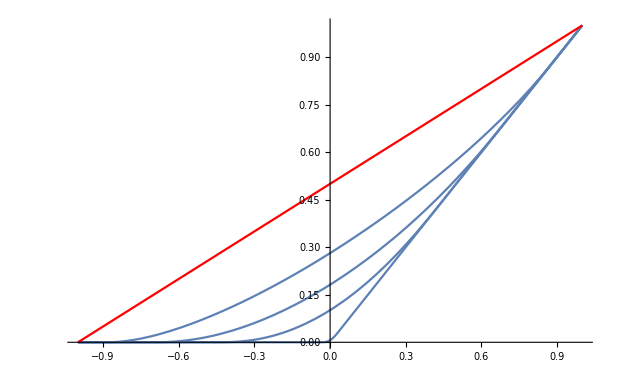

```mathematica
Show[Plot[irradiance[CosTheta,0.001]/0.001,{CosTheta,-1,1}],
Plot[irradiance[CosTheta,0.2]/0.2,{CosTheta,-1,1}],
Plot[irradiance[CosTheta,0.5]/0.5,{CosTheta,-1,1}],
Plot[irradiance[CosTheta,0.8]/0.8,{CosTheta,-1,1}],
Plot[irradiance[CosTheta,1],{CosTheta,-1,1},PlotStyle->Red]
]
```

```mathematica
test=Function[{x,y},
Max[0,(x+y)/(1+y)]
];
Manipulate[Plot[test[x,a],{x,-1,1},PlotRange->{0,1}],{a,0,1}]
```

```mathematica
Show[
Plot3D[irradiance[x,y],{x,-1,1},{y,0,1}],
Plot3D[test[x,y-0.2]*y,{x,-1,1},{y,0,1},PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
diff[x_,y_]:=N[Re[irradiance[x,y]]]-N[Re[test[x,y-0.2]*y]];
Plot3D[diff[x,y],{x,-1,1},{y,0,1}]
```

-Graphics3D-

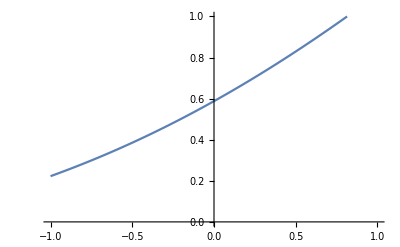

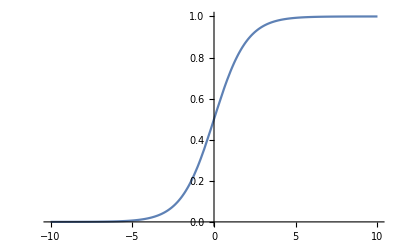

```mathematica
Plot[Log[0.8+Exp[0.8*x]],{x,-1,1},PlotRange->{0,1}]
Plot[Exp[x]/(1+Exp[x]),{x,-10,10},PlotRange->{0,1}]
```

Soft reLu

```mathematica
softreLU[x_,a_]:=1+Log[(ⅇ^(a*x)+1)/(ⅇ^a+1)]/a;
Manipulate[Plot[softreLU[x,a],{x,-1,1},PlotRange->{0,1}],{a,0.001,100}]
```

```mathematica
softreLU2[x_,y_,a_]:=y*softreLU[x,a];
Manipulate[Plot3D[softreLU2[x,y,a],{x,-1,+1},{y,0,1},PlotRange->{0,1}],{a,0.001,20}]
```

Even Even Newer Fitting

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

17

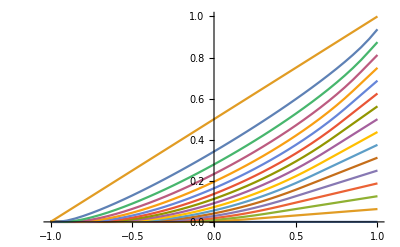

```mathematica
ta=Table[{CosTheta,irradiance[CosTheta,SqSinSigma]},{SqSinSigma,0,1,0.0625},{CosTheta,-1,1,0.05}];
Length[ta]
Show[ListLinePlot[ta,PlotRange->{0,1}]]
```

```mathematica
Clear[x,y,a,b,c,d,e]
index=11;
y=0.0625*index;
model=y*(1+Log[(1+ⅇ^(a x))/(1+ⅇ^a)]/a);
model=y*(1+(Log[1+Exp[a*x]]-Log[1+Exp[a]])/a);
model=softreLU2[x,y,a];
(*NonlinearModelFit[ta[[index]],{model,{a>0}},{a,b,c,d,e},x]*)
FindFit[ta[[index]],{model,{a>0}},{a},x]

(*fit=FindFit[ta[[2]],{model,{a>0}},{a,b,c,d,e},{x,y}]
irradianceApprox2=Function[{x},Evaluate[model/.fit]]*)
```

{a→3.84929}

```mathematica
Clear[a,x,y]
index=0;
FindFit[ta[[1+index]],{model/.y-> 0.0625*index,{a>0}},{a},x]
```

{a→54.8005}

```mathematica
Clear[a,x,y]
fits=Table[a/.FindFit[ta[[1+index]],{model/.y-> 0.0625*index,{a>0}},{a},x],{index,0,Length[ta]-1}]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.33021×10^-8, 5.40646×10^-6, 1.34365×10^-8}, is returned.

{54.8005,52.367,46.9361,34.2208,24.2888,17.204,12.4914,9.29156,6.95717,5.18887,3.84929,2.82976,2.01168,1.29574,0.592661,1.24065×10^-6,5.86338×10^-13}

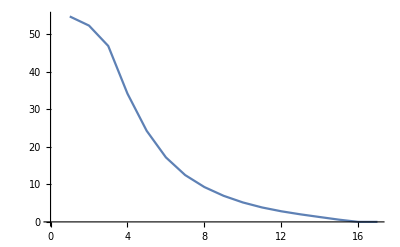

```mathematica
ListLinePlot[fits]
```